# Euclidean curve length and Voronoi regions

Propagating a state through the fast marching algorithm

This notebook illustrates the computation of geodesic euclidean length, and Voronoi regions.
These methods are implemented in the HFMState class, intended to show how a state can be propagated through the Fast Marching Algorithm.

Field verbosity defaults to 1
Field arrayOrdering defaults to RowMajor
Field origin defaults to {0,0}
Field sndOrder defaults to 0
Field showProgress defaults to 0
Field voronoiStoppingCriterion defaults to None
Fast marching solver completed in 0.000244 s.
Field exportActiveNeighs defaults to 0
Field exportGeodesicFlow defaults to 0
Field exportEuclideanLengths defaults to 1
Field euclideanLength_exportGeodesicFromStoppingPoint defaults to 1
Field geodesicSolver defaults to Discrete
Field geodesicStep defaults to 0.25
Field geodesicWeightThreshold defaults to 0.0001
Field geodesicVolumeBound defaults to 4.225
Field exportVoronoiFlags defaults to 1

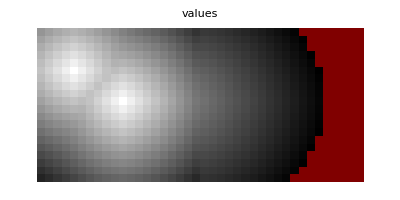

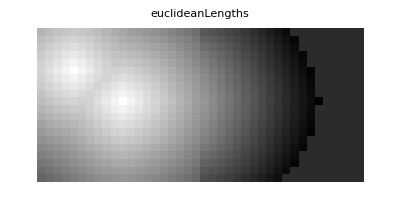

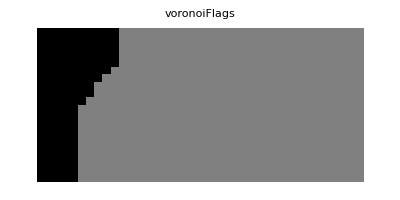

Voronoi flag and euclidean length are set to -1 on non-visited regions

-1. -1.

On the left part of the domain, geodesic length (w.r.t the metric) equals euclidean length

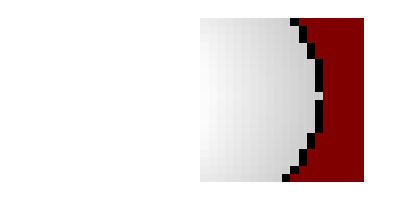

```mathematica
(*To used: Please first execute notebook "Common.nb",in the same directory.*)
Module[{prms,n=20,dims,out,h},
dims={2n,n};
h=1/n;
prms={
(*Setup a very basic fast marching algorithm. The methods illustrated here of course apply to any model.*)
"dims"->dims,
"gridScale"->h,
"seeds"->{{0.5,0.5},{0.2,0.7}},
"speed"->Array[If[#1≤n,1,2]&,dims],
"exportValues"->1,
"progressReportLandmarks"->{},

(*Geodesic euclidean length computation. Define the scale in each grid direction.
For a point dependent scale (e.g. euclidean length on the sphere), use an array*)
"euclideanScale"->h{1,1},
(*Optional stopping criterion, when a geodesic reaches a prescribed length*)
"stopAtEuclideanLength"->1.2,

(*Voronoi diagram computation. Define the flag for each seed.*)
"seedFlags"->{1,2}
};

out=RunExec["FileHFM_Isotropic2",prms]; (*FileHFM_Isotropic also fits*)
Print["log"/.out];
Print[TablePlot["values"/.out,{PlotLabel->"values"}]];
Print[TablePlot["euclideanLengths"/.out,{PlotLabel->"euclideanLengths"}]];
Print[TablePlot["voronoiFlags"/.out,{PlotLabel->"voronoiFlags"}]];

Print["Voronoi flag and euclidean length are set to -1 on non-visited regions"];
Print[Min["euclideanLengths"/.out], " ",Min["voronoiFlags"/.out]];

Print["On the left part of the domain, geodesic length (w.r.t the metric) equals euclidean length"]
Print[TablePlot[("values"/.out)-("euclideanLengths"/.out)]];
];
```